#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[Subscript[r, 1],Subscript[t, 1]].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second beam splitter

```mathematica
{ca1,cc1}=B[Subscript[r, 2],Subscript[t, 2]].{ca2,cc2};
{cd1,cd2}=B[Subscript[r, 2],Subscript[t, 2]].{ca2,cc2};
```

#### Third beam splitter

```mathematica
{cc2,cb2}=B[Subscript[r, 3],Subscript[t, 3]].{cc3,cb3};
ca2=ca3;
```

```mathematica
Collect[ca0,{ca3,cb3,cc3}]
```

ca3 t_1 t_2+cb3 (r_2 r_3 t_1-ⅇ^(-ⅈ ϕ) r_1 t_3)+cc3 (-ⅇ^(-ⅈ ϕ) r_1 r_3-r_2 t_1 t_3)

#### Result

t_1 t_2 a+ (r_2 r_3 t_1-ⅇ^(-ⅈ ϕ)r_1 t_3)b+(-e^(-ⅈ ϕ)r_1 r_3-r_2 t_1 t_3)c

We post select on a being absent.
Unnormalized state is then:
(r_2 r_3 t_1-ⅇ^(-ⅈ ϕ)r_1 t_3)b+(-e^(-ⅈ ϕ)r_1 r_3-r_2 t_1 t_3)c

and  if beam splitters 1 and 3 are 50-50 then:

-(-r_2+ⅇ^(-ⅈ ϕ))/2b+(-r_2-ⅇ^(-ⅈ ϕ))/2 c

V = (I_max-I_min) / (I_max+I_min)

Visibility of interference between b and c

so here the quantity of interest is I=P_b =(|ψ_b|^2)/(|ψ_b|^2+|ψ_c|^2)

```mathematica
FullSimplify[ComplexExpand[Abs[(-Subscript[r, 2]+ⅇ^(-ⅈ ϕ))/2]^2]/(ComplexExpand[Abs[(-Subscript[r, 2]+ⅇ^(-ⅈ ϕ))/2]^2]+ComplexExpand[Abs[(-Subscript[r, 2]-ⅇ^(-ⅈ ϕ))/2]^2])]
```

1/2-(Cos[ϕ] r_2)/(1+r_2^2)

```mathematica
Imax=1/2+Subscript[r, 2]/(1+Subscript[r, 2]^2);
Imin=1/2-Subscript[r, 2]/(1+Subscript[r, 2]^2);
V=(Imax-Imin)/(Imax+Imin)
```

(2 r_2)/(1+r_2^2)

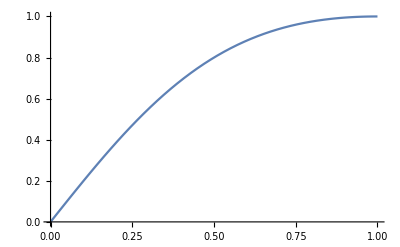

```mathematica
Plot[(2 r)/(1+r^2),{r,0,1}]
```

```mathematica
Manipulate[Plot[1/2-(Cos[ϕ] r)/(1+r^2),{ϕ,0,2π},PlotRange->{0,1}],{r,0,1}]
```

If there was no post selection then the result would be same as when we have r_2→ -1  and t_2→0, giving :

(- r_3 t_1-ⅇ^(-ⅈ ϕ)r_1 t_3)b+(-ⅇ^(-ⅈ ϕ)r_1 r_3+ t_1 t_3)c

If beam splitters 1 and 3 are 50-50 then:

-(1+ⅇ^(-ⅈ ϕ))/2b+(1-ⅇ^(-ⅈ ϕ))/2 c

Visibility of interference between b and c

```mathematica
FullSimplify[(ComplexExpand[Abs[(1+ⅇ^(-ⅈ ϕ))/2]^2]-ComplexExpand[Abs[(1-ⅇ^(-ⅈ ϕ))/2]^2])/(ComplexExpand[Abs[(1+ⅇ^(-ⅈ ϕ))/2]^2]+ComplexExpand[Abs[(1-ⅇ^(-ⅈ ϕ))/2]^2])]
```

Cos[ϕ]

### Adding another beam splitter in the lower path

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[Subscript[r, 1],Subscript[t, 1]].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[Subscript[r, 2],Subscript[t, 2]].{ca2,cc2};
{cb2,cd1}=B[Subscript[r, 4],Subscript[t, 4]].{cb3,cd2};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[Subscript[r, 3],Subscript[t, 3]].{cc3,cd3};
```

### Starting with SMSV in a and b

```mathematica
S[r_,n_]=1/(√Cosh[r])∑_(k=0)^n √Binomial[2k,k](-Tanh[r]/2)^k ca0^(2k)/(√((2k)!));
ClearAll[out]
out[ca2_,cb3_]=Collect[S[r,2],{ca2,cb3,cc3,cd3}];
CoefficientList[out[0,0],{cc3,cd3}][[1;;3,1;;3]]//TableForm
```

1/(√Cosh[r]) | 0 | (-1/2 r_2^2 t_1^2 t_3^2 Tanh[r]-ⅇ^(-ⅈ ϕ) r_1 r_2 r_3 t_1 t_3 t_4 Tanh[r]-1/2 ⅇ^(-2 ⅈ ϕ) r_1^2 r_3^2 t_4^2 Tanh[r])/(√Cosh[r])
0 | (r_2^2 r_3 t_1^2 t_3 Tanh[r]+ⅇ^(-ⅈ ϕ) r_1 r_2 r_3^2 t_1 t_4 Tanh[r]-ⅇ^(-ⅈ ϕ) r_1 r_2 t_1 t_3^2 t_4 Tanh[r]-ⅇ^(-2 ⅈ ϕ) r_1^2 r_3 t_3 t_4^2 Tanh[r])/(√Cosh[r]) | 0
(-1/2 r_2^2 r_3^2 t_1^2 Tanh[r]+ⅇ^(-ⅈ ϕ) r_1 r_2 r_3 t_1 t_3 t_4 Tanh[r]-1/2 ⅇ^(-2 ⅈ ϕ) r_1^2 t_3^2 t_4^2 Tanh[r])/(√Cosh[r]) | 0 | (3/4 r_2^4 r_3^2 t_1^4 t_3^2 Tanh[r]^2+3/2 ⅇ^(-ⅈ ϕ) r_1 r_2^3 r_3^3 t_1^3 t_3 t_4 Tanh[r]^2-3/2 ⅇ^(-ⅈ ϕ) r_1 r_2^3 r_3 t_1^3 t_3^3 t_4 Tanh[r]^2+3/4 ⅇ^(-2 ⅈ ϕ) r_1^2 r_2^2 r_3^4 t_1^2 t_4^2 Tanh[r]^2-3 ⅇ^(-2 ⅈ ϕ) r_1^2 r_2^2 r_3^2 t_1^2 t_3^2 t_4^2 Tanh[r]^2+3/4 ⅇ^(-2 ⅈ ϕ) r_1^2 r_2^2 t_1^2 t_3^4 t_4^2 Tanh[r]^2-3/2 ⅇ^(-3 ⅈ ϕ) r_1^3 r_2 r_3^3 t_1 t_3 t_4^3 Tanh[r]^2+3/2 ⅇ^(-3 ⅈ ϕ) r_1^3 r_2 r_3 t_1 t_3^3 t_4^3 Tanh[r]^2+3/4 ⅇ^(-4 ⅈ ϕ) r_1^4 r_3^2 t_3^2 t_4^4 Tanh[r]^2)/(√Cosh[r])

### Starting with 1_a state

```mathematica
Collect[ca0,{ca3,cb3,cc3}]
```

-cd1 ⅇ^(-ⅈ ϕ) r_1 r_4+ca3 t_1 t_2+cc3 (-r_2 t_1 t_3-ⅇ^(-ⅈ ϕ) r_1 r_3 t_4)+cb3 (r_2 r_3 t_1-ⅇ^(-ⅈ ϕ) r_1 t_3 t_4)

#### Result

-ⅇ^(-ⅈ ϕ) r_1 r_4 d+t_1 t_2 a+ (r_2 r_3 t_1-ⅇ^(-ⅈ ϕ) r_1 t_3 t_4)b+(-ⅇ^(-ⅈ ϕ) r_1 r_3 t_4-r_2 t_1 t_3)c

We post select on aand d being absent.
Unnormalized state is then:
(r_2 r_3 t_1-ⅇ^(-ⅈ ϕ) r_1 t_3 t_4)b+(-ⅇ^(-ⅈ ϕ) r_1 r_3 t_4-r_2 t_1 t_3)c

and  if beam splitters 1 and 3 are 50-50 then:

-(-r_2+ⅇ^(-ⅈ ϕ)t_4)/2b+(-r_2-ⅇ^(-ⅈ ϕ)t_4)/2 c

and  if beam splitters 2 and 4 are also 50 - 50 then :

-(-1+ⅇ^(-ⅈ ϕ))/4b+(-1-ⅇ^(-ⅈ ϕ))/4 c

V = (I_max-I_min) / (I_max+I_min)

Visibility of interference between b and c

so here the quantity of interest is I=P_b

```mathematica
FullSimplify[ComplexExpand[Abs[(-1+ⅇ^(-ⅈ ϕ))/4]^2]/(ComplexExpand[Abs[(-1+ⅇ^(-ⅈ ϕ))/4]^2]+ComplexExpand[Abs[(-1-ⅇ^(-ⅈ ϕ))/4]^2])]
```

Sin[ϕ/2]^2

```mathematica
Imax=1;
Imin=0;
V=(Imax-Imin)/(Imax+Imin)
```

1